```mathematica
(* The list of prime factors of n *)
PrimeFactors[n_Integer]:=Flatten[Take[Transpose[FactorInteger[n]],1]];

(* The index [\Gamma:\Gamma_0(n)];*)

GG0Index[n_Integer]:=
Module[{l,s,i},
l=PrimeFactors[n];
s=n;
For[i=1,i<=Length[l],i++,
s*=1+1/l[[i]];
];
Return[s];
];
(* The number of order-2 and order-3 cone points;*)
(*Note that the number of ideal triangles in a $\Gamma_0(n)$--special triangle is (GG0Index[n]-v3[n])/3;*)
(*  which is also an upperbound for the iterates *)
v2[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,4]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],4];

If[r==3,Return[0],If[r==1,s*=2]];
];
Return[s];
];
v3[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,9]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],3];

If[r==2,Return[0],If[r==1,s*=2]];
];
Return[s];
];
(* Totient summatory function *)
Summatory[m_Integer]:=Sum[EulerPhi[i],{i,1,m}];
SqStartSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb}];
];
ZeroStartSpPoly[n_Integer]:=
Module[{maxmulti=0,t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value,temp},
iterateMax=(GG0Index[n]-v3[n])/3;
t=1;

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
temp=vw[[j]]^2+vw[[j+1]]^2;
If[Mod[temp,n]==0,
maxmulti=Max[maxmulti,temp];
vb=ReplacePart[vb,j->-2];v2count++;Continue[]
]
];
(* Check if odd *)
If[v3count<v3value,
temp=vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2;
If[Mod[temp,n]==0,maxmulti=Max[maxmulti,temp];vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];


For[j1=j+1,j1<Length[vw],j1++,
temp=vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]];
If[vb[[j1]]==-4&&Mod[temp,n]==0,maxmulti=Max[maxmulti,temp];vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb,maxmulti}];
];
PrintSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
Print[vw];
Print[vb];
];
Return[{vw,vb}];
];
```

```mathematica
SqMaxSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m<m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb}];
];
```

```mathematica
l1=SqMaxSpPoly[p*q][[1]];
l2=SqStartSpPoly[p*q][[1]];
Max[l1]
Max[l2]
```

1742

47

```mathematica
43^5
```

147008443

```mathematica
Max[l]
```

1742

```mathematica
41*43
```

1763

```mathematica
l4143A=ZeroStartSpPoly[41*43];
```

```mathematica
l4143B=SqStartSpPoly[41*43];
```

```mathematica
Max[l4143A[[1]]]
```

```mathematica
Floor[Sqrt[4/3]Sqrt[41*43]]
```

48

```mathematica
l101and103A=SqStartSpPoly[101*103];
```

```mathematica
Print["43 appears ", Count[l4143B[[1]],43]," times"];
Print["103 appears ", Count[l101and103A[[1]],103]," times"];
```

43 appears 41 times

103 appears 101 times

```mathematica
p=11;q=13;l=SqStartSpPoly[p*q][[1]]
```

{1,13,12,11,10,9,8,7,13,6,11,5,9,13,4,11,7,10,13,3,11,8,13,5,12,7,9,11,13,2,13,11,9,7,12,5,13,8,11,3,13,10,7,11,4,13,9,5,11,6,13,7,8,9,10,11,1}

```mathematica
p=11;q=13;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=17;q=19;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=29;q=31;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=2;q=31;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=41;q=43;
Print["At n = ",p,"*",q,", we see ",q," appears ",  Count[l4143B[[1]],43]," times"];
p=101;q=103;
Print["At n = ",p,"*",q,", we see ",q," appears ",  Count[l101and103A[[1]],103]," times"];
```

At n = 11*13, we see 13 appears 11 times

At n = 17*19, we see 19 appears 17 times

At n = 29*31, we see 31 appears 29 times

At n = 2*31, we see 31 appears 2 times

At n = 41*43, we see 43 appears 41 times

At n = 101*103, we see 103 appears 101 times

```mathematica
Count
```

```mathematica
Max[l101and103A[[1]]]
```

117

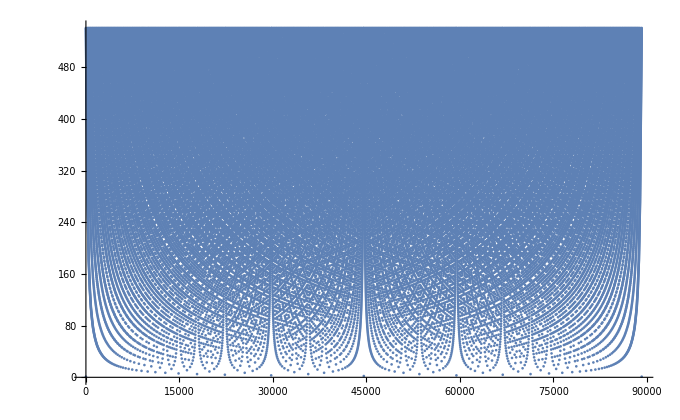

```mathematica
ListPlot[Denominator[FareySequence[p]]]
```

```mathematica
l4143A[[1]]==l4143B[[1]]
```

True

```mathematica
Count[l4143B[[1]],47]
```

6

```mathematica
TwinP={3,5,5,7,11,13,17,19,29,31,41,43,59,61,71,73,101,103,107,109,137,139,149,151,179,181,191,193,197,199,227,229,239,241,269,271,281,283,311,313,347,349,419,421,431,433,461,463,521,523,569,571,599,601,617,619};
```

```mathematica
For[i=1,i<=Length[TwinP]/2,i++,
p=TwinP[[2i-1]];q=TwinP[[2i]];
l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
Print["The max denominator = ",Max[l]];
Print["Floor[Sqrt[4/3 pq]] = ",Floor[Sqrt[4/3 p q]]];
];
```

At n = 3*5, we see 5 appears 3 times

The max denominator = 5

Floor[Sqrt[4/3 pq]] = 4

At n = 5*7, we see 7 appears 5 times

The max denominator = 7

Floor[Sqrt[4/3 pq]] = 6

At n = 11*13, we see 13 appears 11 times

The max denominator = 13

Floor[Sqrt[4/3 pq]] = 13

At n = 17*19, we see 19 appears 17 times

The max denominator = 20

Floor[Sqrt[4/3 pq]] = 20

At n = 29*31, we see 31 appears 29 times

The max denominator = 33

Floor[Sqrt[4/3 pq]] = 34

At n = 41*43, we see 43 appears 41 times

The max denominator = 47

Floor[Sqrt[4/3 pq]] = 48

At n = 59*61, we see 61 appears 59 times

The max denominator = 68

Floor[Sqrt[4/3 pq]] = 69

At n = 71*73, we see 73 appears 71 times

The max denominator = 81

Floor[Sqrt[4/3 pq]] = 83

At n = 101*103, we see 103 appears 101 times

The max denominator = 117

Floor[Sqrt[4/3 pq]] = 117

At n = 107*109, we see 109 appears 107 times

The max denominator = 123

Floor[Sqrt[4/3 pq]] = 124

At n = 137*139, we see 139 appears 137 times

The max denominator = 158

Floor[Sqrt[4/3 pq]] = 159

At n = 149*151, we see 151 appears 149 times

The max denominator = 171

Floor[Sqrt[4/3 pq]] = 173

At n = 179*181, we see 181 appears 179 times

The max denominator = 207

Floor[Sqrt[4/3 pq]] = 207

At n = 191*193, we see 193 appears 191 times

The max denominator = 221

Floor[Sqrt[4/3 pq]] = 221

At n = 197*199, we see 199 appears 197 times

The max denominator = 226

Floor[Sqrt[4/3 pq]] = 228

$Aborted

```mathematica
p=29;q=p+2;
l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
Print["The max denominator = ",max=Max[l]];
Print["Floor[Sqrt[4/3 pq]] = ",Floor[Sqrt[4/3 p q]]];
Print["The max denominator appears ",Count[l,max]," times"];
```

At n = 29*31, we see 31 appears 29 times

The max denominator = 33

Floor[Sqrt[4/3 pq]] = 34

The max denominator appears 4 times

```mathematica
p=11;
For[i=1,i<=5,i++,
Print["p = ",p," and i = ",i," and then p^i case max denom = ",Max[l=SqStartSpPoly[p^i][[1]]]]];
```

p = 7 and i = 1 and then p^i case max denom = 2

p = 7 and i = 2 and then p^i case max denom = 7

p = 7 and i = 3 and then p^i case max denom = 49

p = 7 and i = 4 and then p^i case max denom = 343

$Aborted

```mathematica
p=11;
For[i=1,i<=5,i++,
Print["p = ",p," and i = ",i," and then p^i case max denom = ",Max[l=SqStartSpPoly[p^i][[1]]]]];
```

p = 11 and i = 1 and then p^i case max denom = 3

p = 11 and i = 2 and then p^i case max denom = 12

p = 11 and i = 3 and then p^i case max denom = 121

p = 11 and i = 4 and then p^i case max denom = 1331

$Aborted

```mathematica
p=11;
For[i=1,i<=3,i++,
Print["p = ",p," and i = ",i," and then p^i case max denom = ",Max[l=SqStartSpPoly[p^i][[1]]]]];
```

p = 11 and i = 1 and then p^i case max denom = 3

p = 11 and i = 2 and then p^i case max denom = 12

p = 11 and i = 3 and then p^i case max denom = 121

```mathematica
i=3;l2=SqStartSpPoly[p^i];
```

```mathematica
l2[[2]]
```

{1,2,3,4,5,6,222,7,8,9,10,11,12,135,13,14,15,187,188,115,116,144,221,233,233,223,16,17,18,19,20,21,191,192,182,155,117,118,156,22,20,23,24,148,25,122,187,183,26,217,119,160,27,132,195,24,28,162,151,139,120,121,16,29,30,31,32,223,213,33,34,35,219,234,234,225,36,37,122,123,166,38,39,40,41,128,173,174,197,124,125,37,42,43,30,3,220,44,199,45,46,126,127,168,32,175,46,47,9,153,142,175,176,48,163,14,128,129,170,49,50,51,193,208,39,49,130,131,4,52,201,205,125,207,227,177,52,193,194,158,132,226,214,159,53,54,216,55,50,212,12,5,56,57,204,15,133,134,171,58,59,60,210,146,135,136,178,231,235,235,208,152,61,34,62,63,42,64,232,205,137,138,217,236,236,227,65,117,174,44,195,196,66,67,121,203,230,139,68,69,70,211,237,237,229,43,71,10,72,73,185,140,141,124,141,192,31,68,178,179,189,74,75,76,77,143,142,64,59,8,78,26,79,179,80,214,66,18,81,62,82,116,144,145,70,83,35,84,85,215,61,180,41,86,22,87,88,89,147,146,36,17,67,65,188,180,181,90,91,197,198,149,164,149,148,173,13,7,92,29,93,230,238,238,212,82,33,90,150,229,204,169,75,85,199,200,94,186,172,74,228,239,239,218,152,151,206,231,89,95,60,83,96,80,138,209,240,240,232,181,153,154,143,207,63,88,40,118,156,155,97,203,51,53,98,99,211,100,6,213,48,56,131,215,225,157,130,201,202,101,182,228,210,165,206,194,101,102,159,158,103,104,209,202,57,100,103,119,160,161,105,126,54,183,184,147,136,106,28,107,184,108,120,162,163,107,23,196,94,219,109,110,93,95,111,165,164,191,186,185,161,79,58,104,21,123,166,167,111,77,226,241,241,220,81,96,69,216,224,108,91,110,71,112,169,168,150,137,127,47,113,200,157,19,129,170,218,86,176,190,189,167,11,140,113,45,114,78,134,171,172,133,177,198,38,114,27,84,76,112,224,242,242,222,115,145,190,97,105,73,154,99,25,92,106,87,72,221,55,98,102,109,1,2}

```mathematica
l
```

{1,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,39,19,37,18,35,52,121,69,17,33,16,31,15,29,14,41,27,13,25,37,12,35,23,34,11,32,21,31,10,29,19,28,37,9,35,26,17,25,33,8,31,23,15,37,22,29,36,7,34,27,47,20,33,13,32,51,121,70,19,25,31,37,6,35,29,23,17,28,11,38,27,16,37,21,26,31,36,5,34,29,24,19,33,14,37,23,32,9,31,22,35,13,30,17,38,21,25,29,33,37,4,35,31,27,23,19,34,15,26,37,11,29,18,25,32,7,45,38,31,24,41,17,27,37,47,10,33,23,36,13,29,16,35,19,22,25,28,31,34,37,3,35,32,29,26,23,20,37,17,31,76,121,45,14,25,36,11,30,19,27,35,43,8,37,29,50,121,71,21,34,13,31,18,41,23,28,33,5,42,37,32,27,22,17,46,121,75,29,12,31,19,26,33,7,37,30,23,16,25,34,9,38,29,20,31,11,35,24,37,13,28,15,32,17,36,19,21,23,25,27,29,31,33,35,2,37,35,33,31,29,27,25,23,21,19,36,17,32,15,28,13,37,24,35,11,31,20,29,38,9,34,25,41,16,23,30,37,7,33,26,19,31,12,29,75,121,46,17,22,27,32,37,42,5,33,28,23,41,18,31,13,34,21,71,121,50,29,37,8,43,35,27,19,30,11,36,25,14,45,121,76,31,17,37,20,23,26,29,32,35,3,37,34,31,28,25,22,19,35,16,29,13,36,23,33,10,47,37,27,17,41,24,31,38,45,7,32,25,18,29,11,37,26,15,34,19,23,27,31,35,4,37,33,29,25,21,38,17,30,13,35,22,31,9,32,23,37,14,33,19,24,29,34,5,36,31,26,21,37,16,27,38,11,28,17,23,29,35,6,37,31,25,19,70,121,51,32,13,33,20,47,27,34,7,36,29,22,37,15,23,31,8,33,25,17,26,35,9,37,28,19,29,39,10,31,21,32,11,34,23,35,12,37,25,13,27,14,29,15,31,16,33,17,69,121,52,35,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,1}

```mathematica
For[i=5,i<=20,i++,
q=Prime[i];
For[j=1,j<=i,j++,
p=Prime[j];
If[p>3q/4, Break[]];
l=SqStartSpPoly[p*q][[1]];
(*Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];*)
If[q==Max[l],Print["At (p,q) = (",p,",",q,"): ","True!"];,Print["At (p,q) = (",p,",",q,")","False!"]];
];
];
```

At (p,q) = (2,11): True!

At (p,q) = (3,11): True!

At (p,q) = (5,11): True!

At (p,q) = (7,11): True!

At (p,q) = (2,13): True!

At (p,q) = (3,13): True!

At (p,q) = (5,13): True!

At (p,q) = (7,13): True!

At (p,q) = (2,17): True!

At (p,q) = (3,17): True!

At (p,q) = (5,17): True!

At (p,q) = (7,17): True!

At (p,q) = (11,17): True!

At (p,q) = (2,19): True!

At (p,q) = (3,19): True!

At (p,q) = (5,19): True!

At (p,q) = (7,19): True!

At (p,q) = (11,19): True!

At (p,q) = (13,19): True!

At (p,q) = (2,23): True!

At (p,q) = (3,23): True!

At (p,q) = (5,23): True!

At (p,q) = (7,23): True!

At (p,q) = (11,23): True!

At (p,q) = (13,23): True!

At (p,q) = (17,23): True!

At (p,q) = (2,29): True!

At (p,q) = (3,29): True!

At (p,q) = (5,29): True!

At (p,q) = (7,29): True!

At (p,q) = (11,29): True!

At (p,q) = (13,29): True!

At (p,q) = (17,29): True!

At (p,q) = (19,29): True!

At (p,q) = (2,31): True!

At (p,q) = (3,31): True!

At (p,q) = (5,31): True!

At (p,q) = (7,31): True!

At (p,q) = (11,31): True!

At (p,q) = (13,31): True!

At (p,q) = (17,31): True!

At (p,q) = (19,31): True!

At (p,q) = (23,31): True!

At (p,q) = (2,37): True!

At (p,q) = (3,37): True!

At (p,q) = (5,37): True!

At (p,q) = (7,37): True!

At (p,q) = (11,37): True!

At (p,q) = (13,37): True!

At (p,q) = (17,37): True!

At (p,q) = (19,37): True!

At (p,q) = (23,37): True!

At (p,q) = (2,41): True!

At (p,q) = (3,41): True!

At (p,q) = (5,41): True!

At (p,q) = (7,41): True!

At (p,q) = (11,41): True!

At (p,q) = (13,41): True!

At (p,q) = (17,41): True!

At (p,q) = (19,41): True!

At (p,q) = (23,41): True!

At (p,q) = (29,41): True!

At (p,q) = (2,43): True!

At (p,q) = (3,43): True!

At (p,q) = (5,43): True!

At (p,q) = (7,43): True!

At (p,q) = (11,43): True!

At (p,q) = (13,43): True!

At (p,q) = (17,43): True!

At (p,q) = (19,43): True!

At (p,q) = (23,43): True!

At (p,q) = (29,43): True!

At (p,q) = (31,43): True!

At (p,q) = (2,47): True!

At (p,q) = (3,47): True!

At (p,q) = (5,47): True!

At (p,q) = (7,47): True!

At (p,q) = (11,47): True!

At (p,q) = (13,47): True!

At (p,q) = (17,47): True!

At (p,q) = (19,47): True!

At (p,q) = (23,47): True!

At (p,q) = (29,47): True!

At (p,q) = (31,47): True!

At (p,q) = (2,53): True!

At (p,q) = (3,53): True!

At (p,q) = (5,53): True!

At (p,q) = (7,53): True!

At (p,q) = (11,53): True!

At (p,q) = (13,53): True!

At (p,q) = (17,53): True!

At (p,q) = (19,53): True!

At (p,q) = (23,53): True!

At (p,q) = (29,53): True!

At (p,q) = (31,53): True!

At (p,q) = (37,53): True!

At (p,q) = (2,59): True!

At (p,q) = (3,59): True!

At (p,q) = (5,59): True!

At (p,q) = (7,59): True!

At (p,q) = (11,59): True!

At (p,q) = (13,59): True!

At (p,q) = (17,59): True!

At (p,q) = (19,59): True!

At (p,q) = (23,59): True!

At (p,q) = (29,59): True!

At (p,q) = (31,59): True!

At (p,q) = (37,59): True!

At (p,q) = (41,59): True!

At (p,q) = (43,59): True!

At (p,q) = (2,61): True!

At (p,q) = (3,61): True!

At (p,q) = (5,61): True!

At (p,q) = (7,61): True!

At (p,q) = (11,61): True!

At (p,q) = (13,61): True!

At (p,q) = (17,61): True!

At (p,q) = (19,61): True!

At (p,q) = (23,61): True!

At (p,q) = (29,61): True!

At (p,q) = (31,61): True!

At (p,q) = (37,61): True!

At (p,q) = (41,61): True!

At (p,q) = (43,61): True!

At (p,q) = (2,67): True!

At (p,q) = (3,67): True!

At (p,q) = (5,67): True!

At (p,q) = (7,67): True!

At (p,q) = (11,67): True!

At (p,q) = (13,67): True!

At (p,q) = (17,67): True!

At (p,q) = (19,67): True!

At (p,q) = (23,67): True!

At (p,q) = (29,67): True!

At (p,q) = (31,67): True!

At (p,q) = (37,67): True!

At (p,q) = (41,67): True!

At (p,q) = (43,67): True!

At (p,q) = (47,67): True!

At (p,q) = (2,71): True!

At (p,q) = (3,71): True!

At (p,q) = (5,71): True!

At (p,q) = (7,71): True!

At (p,q) = (11,71): True!

At (p,q) = (13,71): True!

At (p,q) = (17,71): True!

At (p,q) = (19,71): True!

$Aborted

101

```mathematica
l
```

{1,8,7,6,5,14,23,9,4,3,5,7,9,2,7,5,3,13,23,10,7,4,5,6,1}

```mathematica
l
```

{1,5,4,3,8,13,5,2,5,13,8,3,4,5,1}

```mathematica
For[i=5,i<=20,i++,
q=Prime[i];
For[j=1,j<=i,j++,
p=Prime[j];
If[p<3q/4, Continue[]];
l=SqStartSpPoly[p*q][[1]];
(*Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];*)
If[q==Max[l],Print["At (p,q) = (",p,",",q,"): ","True!"];,Print["At (p,q) = (",p,",",q,")","False!"]];
];
];
```

At (p,q) = (11,11)False!

At (p,q) = (11,13): True!

At (p,q) = (13,13)False!

At (p,q) = (13,17): True!

At (p,q) = (17,17)False!

At (p,q) = (17,19)False!

At (p,q) = (19,19)False!

At (p,q) = (19,23): True!

At (p,q) = (23,23)False!

At (p,q) = (23,29): True!

At (p,q) = (29,29)False!

At (p,q) = (29,31)False!

At (p,q) = (31,31)False!

At (p,q) = (29,37): True!

At (p,q) = (31,37): True!

At (p,q) = (37,37)False!

At (p,q) = (31,41): True!

At (p,q) = (37,41)False!

At (p,q) = (41,41)False!

At (p,q) = (37,43)False!

At (p,q) = (41,43)False!

At (p,q) = (43,43)False!

At (p,q) = (37,47): True!

At (p,q) = (41,47)False!

At (p,q) = (43,47)False!

At (p,q) = (47,47)False!

At (p,q) = (41,53): True!

At (p,q) = (43,53): True!

At (p,q) = (47,53)False!

At (p,q) = (53,53)False!

At (p,q) = (47,59): True!

At (p,q) = (53,59)False!

At (p,q) = (59,59)False!

At (p,q) = (47,61): True!

At (p,q) = (53,61)False!

At (p,q) = (59,61)False!

At (p,q) = (61,61)False!

At (p,q) = (53,67)False!

At (p,q) = (59,67)False!

At (p,q) = (61,67)False!

At (p,q) = (67,67)False!

At (p,q) = (59,71)False!

At (p,q) = (61,71)False!

At (p,q) = (67,71)False!

At (p,q) = (71,71)False!

```mathematica
SumTripleSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

];
Return[{vw,vb}];
];
```

```mathematica
SumTripleSpPoly[203][[2]]
```

{-4,1,2,3,4,-4,5,1,6,4,7,2,8,9,10,-4,-4,-4,11,7,-4,6,12,10,-4,13,-4,14,15,-4,5,-4,-4,16,-4,12,8,-4,3,-4,17,15,18,-4,19,9,-4,-4,-4,17,11,14,20,19,21,18,22,16,-4,21,13,20,22,-4}

```mathematica
Prime[17]
```

59

```mathematica
SqStartSpPoly[23][[1]]
```

{1,5,4,3,2,5,3,4,1}

```mathematica
SqStartSpPoly[23][[2]]
```

{1,2,3,2,3,4,1,4}

```mathematica
Prime[9]
```

23

```mathematica
Prime[200]
```

1223

$Aborted

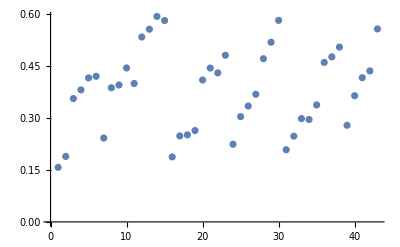

-Graphics-

```mathematica
l0={};
For[n=100,n<=200,n++,
l=SumTripleSpPoly[Prime[n]];
(*Print[l[[1]]];
Print[l[[2]]];*)
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4,s+=1/(l[[1]][[i]]l[[1]][[i+1]])];
];
AppendTo[l0,s//N];
];
ListPlot[l0]
```

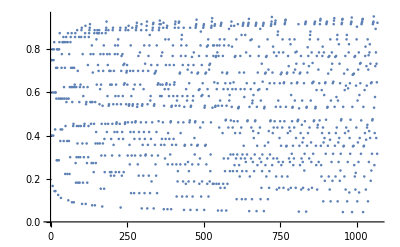

```mathematica
l0={};
For[n=10,n<=100,n++,
l=SumTripleSpPoly[Prime[n]];
(*Print[l[[1]]];
Print[l[[2]]];*)
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4&&((r=l[[1]][[i]]/l[[1]][[i+1]])<1),AppendTo[l0,r]];
];
];
ListPlot[l0]
```

```mathematica
l0
```

{0.1,1.16667,1.2,0.571429,3.33333,0.375,1.6,0.777778,4.5,0.222222,1.28571,0.625,2.66667,0.3,1.75,0.833333,0.857143,10.}

```mathematica
Prime[195]
```

1187

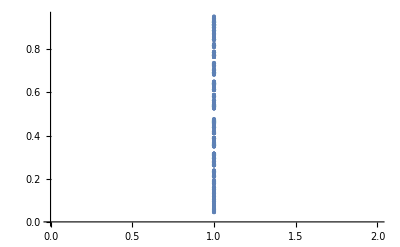

```mathematica
l0={};
For[n=35,n<=100,n++,
l=SumTripleSpPoly[Prime[n]];
(*Print[l[[1]]];
Print[l[[2]]];*)
len=Length[l[[2]]];
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4&&((r=l[[1]][[i]]/l[[1]][[i+1]])<1),AppendTo[l0,r]];
];
];
l1={};
For[i=1,i<=Length[l0],i++,
AppendTo[l1,{1,l0[[i]]}]
];
ListPlot[l1]
```

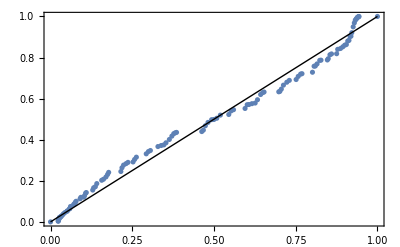

```mathematica
ProbabilityPlot[l0]
```

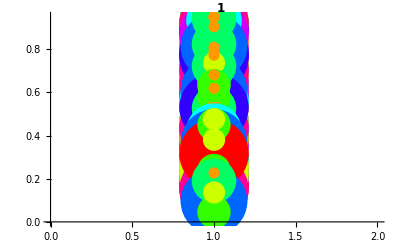

```mathematica
ListPlot[Labeled[Style[#1,PointSize[#2/50],Hue[#2/10]],Style[#2,Bold,12]]&@@@(Tally[l1])]
```

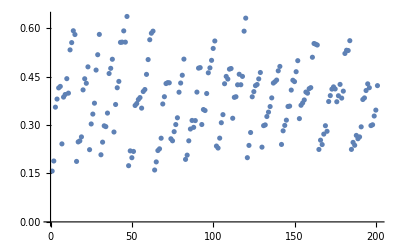

```mathematica
l0={};
For[n=100,n<=300,n++,
l=SumTriple[Prime[n]];
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4,s+=1/(l[[1]][[i]]l[[1]][[i+1]])];
];
AppendTo[l0,s//N];
];
ListPlot[l0]
```

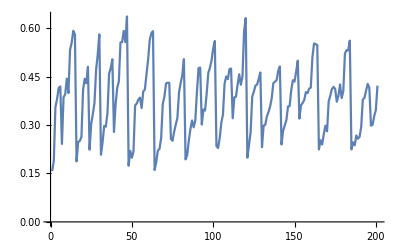

```mathematica
ListLinePlot[l0]
```

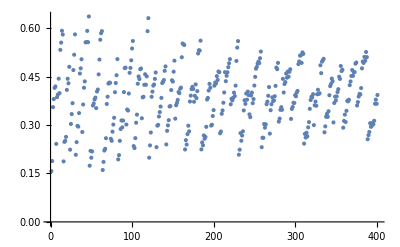

```mathematica
l0={};
For[n=100,n<=00,n++,
l=SumTriple[Prime[n]];
len=Length[l[[2]]];
s=0;
For[i=1,i<=len,i++,
If[l[[2]][[i]]==-4,s+=1/(l[[1]][[i]]l[[1]][[i+1]])];
];
AppendTo[l0,s//N];
];
ListPlot[l0]
```

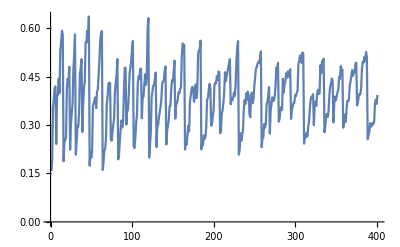

```mathematica
ListLinePlot[l0]
```

```mathematica
l
```

{{1,4,3,2,3,4,1},{0,-4,-4,0,0,-4}}

```mathematica
l0
```

{0.5}

```mathematica
SumTriple[n_Integer]:=
Module[{t,iterateMax,v,iterate,vw,vb,vn,x0,y0,a,b,ap,bp,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,lF,v2count=0,v3count=0,v2value,v3value,FreeSides},
iterateMax=(GG0Index[n]-v3[n])/3;
v=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];
FreeSides={};
lF=FareySequence[v];
vw=Denominator[lF];
vn=Numerator[lF];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
a=vw[[j]];
b=vw[[j+1]];
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[a^2+b^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[a^2+a b+b^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];

ap=vn[[j]];
bp=vn[[j+1]];
x0=n bp;y0=-n ap;
t=Ceiling[(x0-v)/b];
x0=x0-b t;
y0=y0 + a t;
If[y0<= v,vb=ReplacePart[vb,j->0]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

];
Return[{vw,vb}];
];
```

```mathematica
SumTriple[23]
```

{{1,4,3,2,3,4,1},{-4,-4,-4,-4,-4,-4}}

```mathematica
ZeroStartSpPoly[14]
```

{{1,4,7,3,2,3,7,4,1},{1,3,4,2,1,4,3,2}}

```mathematica
For[i=1,i<=20,i++,
q=Prime[i];
NN=2 q;
l=ZeroStartSpPoly[NN];
Print["q = ", q," and Max denom = ",Max[l[[1]]]," and max multiplier = ",l[[3]]];



];
```

q = 2 and Max denom = 2 and max multiplier = 4

q = 3 and Max denom = 3 and max multiplier = 12

q = 5 and Max denom = 5 and max multiplier = 30

q = 7 and Max denom = 7 and max multiplier = 56

q = 11 and Max denom = 11 and max multiplier = 132

q = 13 and Max denom = 13 and max multiplier = 208

q = 17 and Max denom = 17 and max multiplier = 306

q = 19 and Max denom = 19 and max multiplier = 456

q = 23 and Max denom = 23 and max multiplier = 552

q = 29 and Max denom = 29 and max multiplier = 986

q = 31 and Max denom = 31 and max multiplier = 992

q = 37 and Max denom = 37 and max multiplier = 1628

q = 41 and Max denom = 41 and max multiplier = 1968

q = 43 and Max denom = 43 and max multiplier = 2236

q = 47 and Max denom = 47 and max multiplier = 2632

q = 53 and Max denom = 53 and max multiplier = 2862

q = 59 and Max denom = 59 and max multiplier = 4130

q = 61 and Max denom = 61 and max multiplier = 4392

q = 67 and Max denom = 67 and max multiplier = 5494

q = 71 and Max denom = 71 and max multiplier = 5254